```mathematica
nu=mun (V/H)^(n-1)/rho;
```

```mathematica
veqn=V==gp H^2 So /nu//Simplify
```

V==(gp H rho So V (V/H)^-n)/mun

```mathematica
Solve[veqn, V]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{V→0},{V→H ((gp H rho So)/mun)^(1/n)}}

```mathematica
U=n/(n+1) ((rho gp So)/mun)^(1/n) H^((n+1)/n) (1-B)^((n+1)/n) (1-n/(2n+1) (1-B))
```

((1-B)^((1+n)/n) H^((1+n)/n) n (1-((1-B) n)/(1+2 n)) ((gp rho So)/mun)^(1/n))/(1+n)

```mathematica
(V/U)/.{V->H ((gp H rho So)/mun)^(1/n)}//FullSimplify
```

((1-B)^(-1-1/n) H^(-1/n) (1+n) (1+2 n) ((gp rho So)/mun)^(-1/n) ((gp H rho So)/mun)^(1/n))/(n (1+n+B n))

```mathematica
Assuming[{H∈PositiveReals, mun∈PositiveReals, n∈PositiveReals, gp∈PositiveReals, rho∈PositiveReals}, FullSimplify[(V/U)/.{V->H ((gp H rho So)/mun)^(1/n)}]]
```

((1-B)^(-1-1/n) (1+n) (1+2 n))/(n (1+n+B n))

```mathematica
reBal=((V H^2)/(nu (H/So)))/.{V->(U  (((1-B)^(-1-1/n) (1+n) (1+2 n))/(n (1+n+B n))))}//Simplify
```

(H^2 rho So (H^(1/n) ((gp rho So)/mun)^(1/n))^(2-n))/mun

```mathematica
re=(rho H^n U^(2-n))/mun//Simplify
```

(H^n rho (((1-B)^(1+1/n) H^(1+1/n) n (1+n+B n) ((gp rho So)/mun)^(1/n))/((1+n) (1+2 n)))^(2-n))/mun

```mathematica
Assuming[{H∈PositiveReals, mun∈PositiveReals, n∈PositiveReals, gp∈PositiveReals, rho∈PositiveReals,  So∈PositiveReals}, FullSimplify[reBal/re]]
```

(((1-B)^(1+1/n) n (1+n+B n))/((1+n) (1+2 n)))^(-2+n) So

```mathematica
rec=(((1+n+2 n  B(1+ n  B)) (1+n)(2+n)(2+3n) (1-B)^(-2/n))/(2(2+n)(1+n)^2+n (2+n)(7+9n)B+(11+19n+6 n^2)(2+n B)n^2 B^2))/((((1-B)^(1+1/n) n (1+n+B n))/((1+n) (1+2 n)))^(-2+n) So)//Simplify
```

((1-B)^(-2/n) (1+n) (2+n) (2+3 n) (((1-B)^(1+1/n) n (1+n+B n))/((1+n) (1+2 n)))^(2-n) (1+n+2 B n (1+B n)))/((2 (1+n)^2 (2+n)+B n (2+n) (7+9 n)+B^2 n^2 (2+B n) (11+19 n+6 n^2)) So)

```mathematica
Assuming[{H∈PositiveReals, mun∈PositiveReals, n∈PositiveReals, gp∈PositiveReals, rho∈PositiveReals,  So∈PositiveReals}, FullSimplify[(recVar==((1-B)^(-2/n) (1+n) (2+n) (2+3 n) (((1-B)^(1+1/n) n (1+n+B n))/((1+n) (1+2 n)))^(2-n) (1+n+2 B n (1+B n)))/((2 (1+n)^2 (2+n)+B n (2+n) (7+9 n)+B^2 n^2 (2+B n) (11+19 n+6 n^2)) So))/.{So->(((((1-B)^(1+1/n) (1/fr^2)^(1/n) n (1+n+B n))/((1+n) (1+2 n)))^-n)/recVar)}]]
```

recVar==((1-B)^(-2/n) n^2 (2+n) (2+3 n) ((1-B)^(1+1/n) (1+n+B n))^(2-n) ((1-B)^(1+1/n) (1/fr^2)^(1/n) (1+n+B n))^n (1+n+2 B n (1+B n)) recVar)/((1+n) (1+2 n)^2 (2 (1+n)^2 (2+n)+B n (2+n) (7+9 n)+B^2 n^2 (2+B n) (11+n (19+6 n))))

```mathematica
frSol=√(((1-B)^(-2/n) n^2 (2+n) (2+3 n) ((1-B)^(1+1/n) (1+n+B n))^(2-n) ((1-B)^(1+1/n)   (1+n+B n))^n (1+n+2 B n (1+B n)))/((1+n) (1+2 n)^2 (2 (1+n)^2 (2+n)+B n (2+n) (7+9 n)+B^2 n^2 (2+B n) (11+n (19+6 n)))))
```

√(((1-B)^2 n^2 (2+n) (2+3 n) (1+n+B n)^2 (1+n+2 B n (1+B n)))/((1+n) (1+2 n)^2 (2 (1+n)^2 (2+n)+B n (2+n) (7+9 n)+B^2 n^2 (2+B n) (11+n (19+6 n)))))

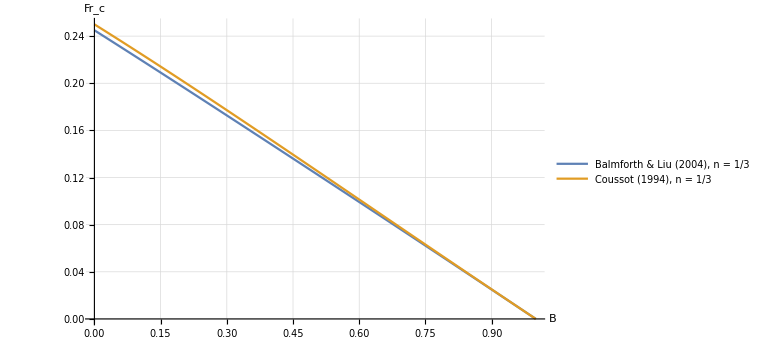

```mathematica
Plot[{frSol/.{n->1/3},(((1/n+1)(1/B)^2-(1/n)(1/B)-1)/((1/n+1)^2(1/B)^2+(1/n)(1/B)+1))/.{n->1/3}}, {B,0,1}, PlotLegends->{Style["Balmforth & Liu (2004), n = 1/3", 22,FontFamily->"Times"],Style["Coussot (1994), n = 1/3",22,FontFamily->"Times"]},GridLines->Automatic, AxesLabel->{Style["B",23, Italic,FontFamily->"Times"],Style["Fr_c", 23,FontFamily->"Times"]},GridLines->Automatic, PlotRange->{{0,1}, {0, Automatic}},ImageSize->Large,PlotPoints->100,TicksStyle->{{FontSize->20,FontFamily->"Times"},{FontSize->20,FontFamily->"Times"}} ]
```